# Expansión cercana a 0

```mathematica
frees=1+r^2+((-1085 r^6-(441 r^2 μ)/2+3/2 √7 r^2 √(532656 r^8+30380 r^4 μ+3087 μ^2))^(1/3))/7^(2/3)-(101 (2/7)^(1/3) r^4)/((-2170 r^6-441 r^2 μ+3 √7 r^2 √(532656 r^8+30380 r^4 μ+3087 μ^2))^(1/3))
```

1+r^2+((-1085 r^6-(441 r^2 μ)/2+3/2 √7 r^2 √(532656 r^8+30380 r^4 μ+3087 μ^2))^(1/3))/7^(2/3)-(101 (2/7)^(1/3) r^4)/((-2170 r^6-441 r^2 μ+3 √7 r^2 √(532656 r^8+30380 r^4 μ+3087 μ^2))^(1/3))

```mathematica
Assuming[r>0&&μ>0,Simplify[Series[Simplify[frees],{r,0,2}]]]
```

1-3^(2/3) μ^(1/3) r^(2/3)+r^2+O[r]^(7/3)

```mathematica
(frees-1)^2
```

(r^2+((-1085 r^6-(441 r^2 μ)/2+3/2 √7 r^2 √(532656 r^8+30380 r^4 μ+3087 μ^2))^(1/3))/7^(2/3)-(101 (2/7)^(1/3) r^4)/((-2170 r^6-441 r^2 μ+3 √7 r^2 √(532656 r^8+30380 r^4 μ+3087 μ^2))^(1/3)))^2

```mathematica
Assuming[r>0&&μ>0,Simplify[Series[Simplify[(frees-1)^2],{r,0,2}]]]
```

3 3^(1/3) μ^(2/3) r^(4/3)-2 (3^(2/3) μ^(1/3)) r^(8/3)+O[r]^3

### Primera derivada de f

```mathematica
der1f=Simplify[D[frees,r]]
```

2 r-(404 (2/7)^(1/3) r^3)/((r^2 (-2170 r^4-441 μ+3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2)))^(1/3))+((2/7)^(2/3) (-6510 r^5-441 r μ+(12 r^5 (266328 r^4+7595 μ))/(√((532656 r^8)/7+4340 r^4 μ+441 μ^2))+3 √7 r √(532656 r^8+30380 r^4 μ+3087 μ^2)))/(3 (r^2 (-2170 r^4-441 μ+3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2)))^(2/3))+(101 (2/7)^(1/3) r^4 (-13020 r^5-882 r μ+(24 r^5 (266328 r^4+7595 μ))/(√((532656 r^8)/7+4340 r^4 μ+441 μ^2))+6 √7 r √(532656 r^8+30380 r^4 μ+3087 μ^2)))/(3 (r^2 (-2170 r^4-441 μ+3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2)))^(4/3))

```mathematica
Assuming[r>0&&μ>0,Simplify[Series[Simplify[der1f],{r,0,2}]]]
```

-(2 μ^(1/3))/(3^(1/3) r^(1/3))+2 r+O[r]^(7/3)

```mathematica
Simplify[der1f^2]
```

(2 r-(404 (2/7)^(1/3) r^3)/((r^2 (-2170 r^4-441 μ+3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2)))^(1/3))+((2/7)^(2/3) (-6510 r^5-441 r μ+(12 r^5 (266328 r^4+7595 μ))/(√((532656 r^8)/7+4340 r^4 μ+441 μ^2))+3 √7 r √(532656 r^8+30380 r^4 μ+3087 μ^2)))/(3 (r^2 (-2170 r^4-441 μ+3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2)))^(2/3))+(101 (2/7)^(1/3) r^4 (-13020 r^5-882 r μ+(24 r^5 (266328 r^4+7595 μ))/(√((532656 r^8)/7+4340 r^4 μ+441 μ^2))+6 √7 r √(532656 r^8+30380 r^4 μ+3087 μ^2)))/(3 (r^2 (-2170 r^4-441 μ+3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2)))^(4/3)))^2

```mathematica
Assuming[r>0&&μ>0,Simplify[Series[Simplify[der1f^2],{r,0,2}]]]
```

(4 μ^(2/3))/(3^(2/3) r^(2/3))-(8 μ^(1/3) r^(2/3))/3^(1/3)-(3788 r^2)/63+O[r]^(7/3)

### Segunda derivada de f

```mathematica
der2f=Simplify[D[frees,{r,2}]]
```

2-(2 2^(2/3) 7^(1/3) r^2 (263861845332480 √7 r^20+686 r^8 μ^2 (1546212066 √7 μ-67259747 √(532656 r^8+30380 r^4 μ+3087 μ^2))+60760 r^12 μ (201930442 √7 μ-4562587 √(532656 r^8+30380 r^4 μ+3087 μ^2))+46891530 r^4 μ^3 (441 √7 μ-22 √(532656 r^8+30380 r^4 μ+3087 μ^2))+9529569 μ^4 (-21 √7 μ+√(532656 r^8+30380 r^4 μ+3087 μ^2))-1065312 r^16 (-97722506 √7 μ+1366651 √(532656 r^8+30380 r^4 μ+3087 μ^2))))/((532656 r^8+30380 r^4 μ+3087 μ^2)^(3/2) (r^2 (-2170 r^4-441 μ+3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2)))^(5/3))+(404 2^(1/3) 7^(2/3) r^2 (263861845332480 √7 r^20+686 r^8 μ^2 (2314409118 √7 μ-46568723 √(532656 r^8+30380 r^4 μ+3087 μ^2))+425320 r^12 μ (24726002 √7 μ-423517 √(532656 r^8+30380 r^4 μ+3087 μ^2))+46891530 r^4 μ^3 (2457 √7 μ-82 √(532656 r^8+30380 r^4 μ+3087 μ^2))-333534915 μ^4 (-21 √7 μ+√(532656 r^8+30380 r^4 μ+3087 μ^2))-1065312 r^16 (-59456278 √7 μ+1366651 √(532656 r^8+30380 r^4 μ+3087 μ^2))))/((532656 r^8+30380 r^4 μ+3087 μ^2)^(3/2) (2170 r^4+441 μ-3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2))^2 (r^2 (-2170 r^4-441 μ+3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2)))^(1/3))

```mathematica
Assuming[r>0&&μ>0,Simplify[Series[Simplify[der2f],{r,0,2}]]]
```

(2 μ^(1/3))/(3 3^(1/3) r^(4/3))+2+(1010 r^(4/3))/(9 3^(2/3) μ^(1/3))+O[r]^(7/3)

```mathematica
Simplify[der2f^2]
```

(2-(2 2^(2/3) 7^(1/3) r^2 (263861845332480 √7 r^20+686 r^8 μ^2 (1546212066 √7 μ-67259747 √(532656 r^8+30380 r^4 μ+3087 μ^2))+60760 r^12 μ (201930442 √7 μ-4562587 √(532656 r^8+30380 r^4 μ+3087 μ^2))+46891530 r^4 μ^3 (441 √7 μ-22 √(532656 r^8+30380 r^4 μ+3087 μ^2))+9529569 μ^4 (-21 √7 μ+√(532656 r^8+30380 r^4 μ+3087 μ^2))-1065312 r^16 (-97722506 √7 μ+1366651 √(532656 r^8+30380 r^4 μ+3087 μ^2))))/((532656 r^8+30380 r^4 μ+3087 μ^2)^(3/2) (r^2 (-2170 r^4-441 μ+3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2)))^(5/3))+(404 2^(1/3) 7^(2/3) r^2 (263861845332480 √7 r^20+686 r^8 μ^2 (2314409118 √7 μ-46568723 √(532656 r^8+30380 r^4 μ+3087 μ^2))+425320 r^12 μ (24726002 √7 μ-423517 √(532656 r^8+30380 r^4 μ+3087 μ^2))+46891530 r^4 μ^3 (2457 √7 μ-82 √(532656 r^8+30380 r^4 μ+3087 μ^2))-333534915 μ^4 (-21 √7 μ+√(532656 r^8+30380 r^4 μ+3087 μ^2))-1065312 r^16 (-59456278 √7 μ+1366651 √(532656 r^8+30380 r^4 μ+3087 μ^2))))/((532656 r^8+30380 r^4 μ+3087 μ^2)^(3/2) (2170 r^4+441 μ-3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2))^2 (r^2 (-2170 r^4-441 μ+3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2)))^(1/3)))^2

```mathematica
Assuming[r>0&&μ>0,Simplify[Series[Simplify[der2f^2],{r,0,2}]]]
```

(4 μ^(2/3))/(9 3^(2/3) r^(8/3))+(8 μ^(1/3))/(3 3^(1/3) r^(4/3))+4364/81+(81800 r^(4/3))/(243 3^(2/3) μ^(1/3))+(938260 r^(8/3))/(243 3^(1/3) μ^(2/3))+O[r]^3

### Kretschmann

```mathematica
K=Simplify[(12*((frees-1)^2)+6*r^2*der1f^2+r^4*der2f^2)/r^4]
```

1/r^4(12 (r^2-(101 (2/7)^(1/3) r^4)/((r^2 (-2170 r^4-441 μ+3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2)))^(1/3))+((r^2 (-2170 r^4-441 μ+3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2)))^(1/3))/(2^(1/3) 7^(2/3)))^2+6 r^2 (2 r-(404 (2/7)^(1/3) r^3)/((r^2 (-2170 r^4-441 μ+3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2)))^(1/3))+((2/7)^(2/3) (-6510 r^5-441 r μ+(12 r^5 (266328 r^4+7595 μ))/(√((532656 r^8)/7+4340 r^4 μ+441 μ^2))+3 √7 r √(532656 r^8+30380 r^4 μ+3087 μ^2)))/(3 (r^2 (-2170 r^4-441 μ+3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2)))^(2/3))+(101 (2/7)^(1/3) r^4 (-13020 r^5-882 r μ+(24 r^5 (266328 r^4+7595 μ))/(√((532656 r^8)/7+4340 r^4 μ+441 μ^2))+6 √7 r √(532656 r^8+30380 r^4 μ+3087 μ^2)))/(3 (r^2 (-2170 r^4-441 μ+3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2)))^(4/3)))^2+r^4 (2-(2 2^(2/3) 7^(1/3) r^2 (263861845332480 √7 r^20+686 r^8 μ^2 (1546212066 √7 μ-67259747 √(532656 r^8+30380 r^4 μ+3087 μ^2))+60760 r^12 μ (201930442 √7 μ-4562587 √(532656 r^8+30380 r^4 μ+3087 μ^2))+46891530 r^4 μ^3 (441 √7 μ-22 √(532656 r^8+30380 r^4 μ+3087 μ^2))+9529569 μ^4 (-21 √7 μ+√(532656 r^8+30380 r^4 μ+3087 μ^2))-1065312 r^16 (-97722506 √7 μ+1366651 √(532656 r^8+30380 r^4 μ+3087 μ^2))))/((532656 r^8+30380 r^4 μ+3087 μ^2)^(3/2) (r^2 (-2170 r^4-441 μ+3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2)))^(5/3))+(404 2^(1/3) 7^(2/3) r^2 (263861845332480 √7 r^20+686 r^8 μ^2 (2314409118 √7 μ-46568723 √(532656 r^8+30380 r^4 μ+3087 μ^2))+425320 r^12 μ (24726002 √7 μ-423517 √(532656 r^8+30380 r^4 μ+3087 μ^2))+46891530 r^4 μ^3 (2457 √7 μ-82 √(532656 r^8+30380 r^4 μ+3087 μ^2))-333534915 μ^4 (-21 √7 μ+√(532656 r^8+30380 r^4 μ+3087 μ^2))-1065312 r^16 (-59456278 √7 μ+1366651 √(532656 r^8+30380 r^4 μ+3087 μ^2))))/((532656 r^8+30380 r^4 μ+3087 μ^2)^(3/2) (2170 r^4+441 μ-3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2))^2 (r^2 (-2170 r^4-441 μ+3 √7 √(532656 r^8+30380 r^4 μ+3087 μ^2)))^(1/3)))^2)

```mathematica
Assuming[r>0&&μ>0,Simplify[Series[Simplify[K],{r,0,5}]]]
```

(1192 μ^(2/3))/(9 3^(2/3) r^(8/3))-(352 μ^(1/3))/(3 3^(1/3) r^(4/3))-363544/567+(4665152 r^(4/3))/(1701 3^(2/3) μ^(1/3))+(103007272 r^(8/3))/(11907 3^(1/3) μ^(2/3))-(50096000 r^4)/(5103 μ)+O[r]^(16/3)

```mathematica
Kprox=Expand[(12*(3 3^(1/3) μ^(2/3) r^(4/3)-2 (3^(2/3) μ^(1/3)) r^(8/3))+6*r^2*((4 μ^(2/3))/(3^(2/3) r^(2/3))-(8 μ^(1/3) r^(2/3))/3^(1/3)-(3788 r^2)/63)+r^4*((4 μ^(2/3))/(9 3^(2/3) r^(8/3))+(8 μ^(1/3))/(3 3^(1/3) r^(4/3))+4364/81+(81800 r^(4/3))/(243 3^(2/3) μ^(1/3))+(938260 r^(8/3))/(243 3^(1/3) μ^(2/3))))/(r^4)]
```

-174004/567+(938260 r^(8/3))/(243 3^(1/3) μ^(2/3))+(81800 r^(4/3))/(243 3^(2/3) μ^(1/3))-(352 μ^(1/3))/(3 3^(1/3) r^(4/3))+(1192 μ^(2/3))/(9 3^(2/3) r^(8/3))

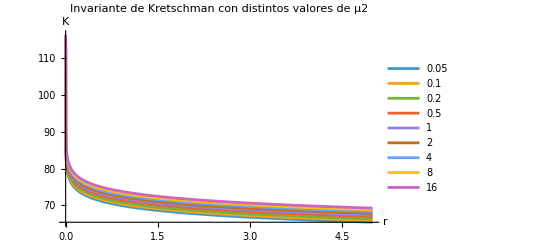

```mathematica
Plot[Evaluate@Table[Log[-363544/567-(352 μ^(1/3))/(3 3^(1/3) r^(4/3))+(1192 μ^(2/3))/(9 3^(2/3) r^(8/3))],{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r,0,0.00000000005},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Invariante de Kretschman con distintos valores de μ2",AxesLabel->{Style["r",18,Bold],Style["K",18,Bold],Style["K",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14]]
```